# MFPT for ballistic walkers

Note that in here ‘nu’ denotes the number of searchers N and u=x/L as denoted in the paper. Tnd is the dimensionless MFPT as in Eqn. (8) of the manuscript.

```mathematica
Tnd[nu_,u_]:=(1/(nu*u*  NIntegrate[(1/(2 τ^2)(ⅇ^(-u/τ)))*(1-1/2 ⅇ^((-(1-u))/τ)-1/2 ⅇ^(-u/τ))^(nu-1),{τ,0,1000},MinRecursion->8]))1/u NIntegrate[(1-1/2 ⅇ^((-(1-u))/τ)-1/2 ⅇ^(-u/τ))^nu,{τ,0,1000},MinRecursion->8]
```

Variation of MFPT  with u for N=7 ballistic searchers

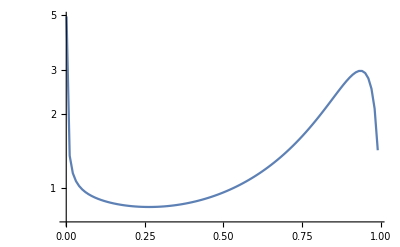

```mathematica
adat=ParallelTable[{u,Tnd[7,u]},{u,0.001,1,1/100}];
aplot2=ListLogPlot[adat,Joined->True]
```

# MFPT for diffusive searchers

```mathematica
TND[nu_,u_]:=NIntegrate[(2Sum[Sin[n π u](-(-1+(-1)^n)/(n π))ⅇ^(-(n^2 π^2 t)),{n,1,10^3}])^nu,{t,0,1000},MinRecursion->8]/(u^2 nu*NIntegrate[(2 Sum[ n π Sin[n π u] ⅇ^(-(n^2 π^2 t)),{n,1,10^3}])((2Sum[Sin[n π u](-(-1+(-1)^n)/(n π))ⅇ^(-(n^2 π^2 t)),{n,1,10^3}])^(nu-1)),{t,0,1000},MinRecursion->8])
```

Variation of the MFPT with u for N=3 diffusive searchers

```mathematica
adat3=ParallelTable[{N[10^u],TND[3,N[10^u]]},{u,-1,-0.02,1/100}];
```

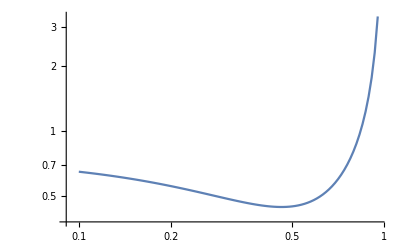

```mathematica
ListLogLogPlot[adat3,Joined->True]
```